```mathematica
(*U(1)*SU(2): as quaternions*)
s[1]={{1,0},{0,1}};
s[2]={{0,1},{-1,0}};
s[3]={{I,0},{0,-I}};
s[4]={{0,I},{I,0}};
```

```mathematica
(*U(1)*SO(2,c)*SU(2)->SO(4)*)
```

```mathematica
(*first ellipse:Roots:{Real, Imaginary,Imaginary}: electric*)
```

```mathematica
(*w[x_]=4*x^3-g2*x-g3*)
```

```mathematica
Sa[1]=s[2]
Sa[2]=s[3]
Sa[3]=s[4]
```

{{0,1},{-1,0}}

{{ⅈ,0},{0,-ⅈ}}

{{0,ⅈ},{ⅈ,0}}

```mathematica
(*second ellipse (hyperbolic):Roots:{Imaginary, Imaginary,Real}:Magnetic*)
```

```mathematica
(*wc[x_]=4*(I*x)^3-g2*I*x-g3*)
```

```mathematica
Sa[4]=I*s[1]
Sa[5]=I*s[2]
Sa[6]=I*s[3]
```

{{ⅈ,0},{0,ⅈ}}

{{0,ⅈ},{-ⅈ,0}}

{{-1,0},{0,1}}

```mathematica
Table[Det[Sa[i]],{i,6}]
```

{1,1,1,-1,-1,-1}

```mathematica
Table[Tr[Sa[i]],{i,6}]
```

{0,0,0,2 ⅈ,0,0}

```mathematica
Sum[Sa[i].Sa[i],{i,6}]
```

{{-2,0},{0,-2}}

```mathematica
(*Killing vectors*)
```

```mathematica
kl=Table[Sa[i].{1,1},{i,6}]
```

{{1,-1},{ⅈ,-ⅈ},{ⅈ,ⅈ},{ⅈ,ⅈ},{ⅈ,-ⅈ},{-1,1}}

```mathematica
kk=kl.Transpose[kl]
```

{{2,2 ⅈ,0,0,2 ⅈ,-2},{2 ⅈ,-2,0,0,-2,-2 ⅈ},{0,0,-2,-2,0,0},{0,0,-2,-2,0,0},{2 ⅈ,-2,0,0,-2,-2 ⅈ},{-2,-2 ⅈ,0,0,-2 ⅈ,2}}

```mathematica
TableForm[kk]
```

2 | 2 ⅈ | 0 | 0 | 2 ⅈ | -2
2 ⅈ | -2 | 0 | 0 | -2 | -2 ⅈ
0 | 0 | -2 | -2 | 0 | 0
0 | 0 | -2 | -2 | 0 | 0
2 ⅈ | -2 | 0 | 0 | -2 | -2 ⅈ
-2 | -2 ⅈ | 0 | 0 | -2 ⅈ | 2

```mathematica
Eigenvalues[kk]
```

{-4,0,0,0,0,0}

```mathematica
CharacteristicPolynomial[kk,x]
```

4 x^5+x^6

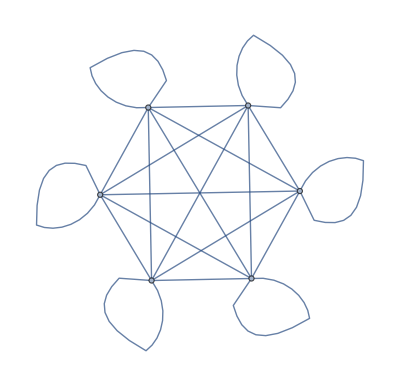

```mathematica
WeightedAdjacencyGraph[kk]
```

```mathematica
(*Cartan matrix*)
```

```mathematica
ca=Table[2*kl[[i]].kl[[j]]/(kl[[i]].kl[[i]]),{i,6},{j,6}]
```

{{2,2 ⅈ,0,0,2 ⅈ,-2},{-2 ⅈ,2,0,0,2,2 ⅈ},{0,0,2,2,0,0},{0,0,2,2,0,0},{-2 ⅈ,2,0,0,2,2 ⅈ},{-2,-2 ⅈ,0,0,-2 ⅈ,2}}

```mathematica
TableForm[ca]
```

2 | 2 ⅈ | 0 | 0 | 2 ⅈ | -2
-2 ⅈ | 2 | 0 | 0 | 2 | 2 ⅈ
0 | 0 | 2 | 2 | 0 | 0
0 | 0 | 2 | 2 | 0 | 0
-2 ⅈ | 2 | 0 | 0 | 2 | 2 ⅈ
-2 | -2 ⅈ | 0 | 0 | -2 ⅈ | 2

```mathematica
Eigenvalues[ca]
```

{8,4,0,0,0,0}

```mathematica
CharacteristicPolynomial[ca,x]
```

32 x^4-12 x^5+x^6

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-